```mathematica
mudis=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-mu-dis-ICARUS-no.dat","Data"];
```

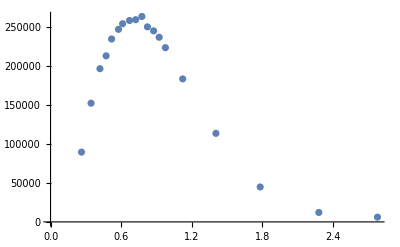

```mathematica
ListPlot[mudis]
```

```mathematica
Sum[mudis[[i,2]]*murate[[i,2]],{i,1,Length[mudis]}]
```

273951.

```mathematica
murate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/sig-bg-SBND/ic-m-sig.dat","Data"];
```

```mathematica
Table[((mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])),{i,1,Length[mudis]}]
```

{0.128549,0.12262,0.123625,0.122478,0.128609,0.13048,0.130887,0.138519,0.143258,0.156467,0.159101,0.167931,0.182456,0.191465,0.215313,0.254951,0.251148,0.182073,0.169885}

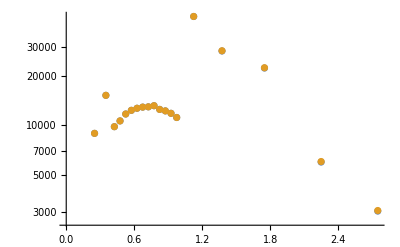

```mathematica
ListLogPlot[{Table[{murate[[i,1]],murate[[i,3]]},{i,1,Length[murate]}],Table[{murate[[i,1]],mudis[[i,2]]*murate[[i,2]]},{i,1,Length[murate]}]}]
```

```mathematica
NMinimize[Sum[((1+a)*murate[[i,3]]-mudis[[i,2]]*murate[[i,2]])^2/(mudis[[i,2]]*murate[[i,2]]),{i,1,Length[murate]}]+(a/0.1)^2+(b/0.1)^2,{a,b}]
```

{1.05308,{a→0.00108502,b→0.}}

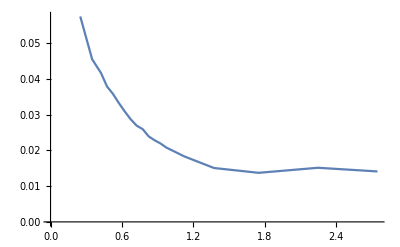

```mathematica
ListPlot[Table[{murate[[i,1]],(mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])},{i,1,Length[mudis]}],Joined->True]
```

```mathematica
murate2=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-mu.dat","Data"];
```

```mathematica
murate
```

{{0.25,0.1,144828,0},{0.35,0.1,302569,0},{0.425,0.05,212305,0},{0.475,0.05,254988,0},{0.525,0.05,297000,0},{0.575,0.05,338569,0},{0.625,0.05,379659,0},{0.675,0.05,417456,0},{0.725,0.05,448730,0},{0.775,0.05,473076,0},{0.825,0.05,491511,0},{0.875,0.05,503980,0},{0.925,0.05,510622,0},{0.975,0.05,511765,0},{1.125,0.25,2.39711×10^6,0},{1.375,0.25,1.80641×10^6,0},{1.75,0.5,1.53437×10^6,0},{2.25,0.5,339281,0},{2.75,0.5,145625,0}}

```mathematica
Table[{murate2[[i,1]],(murate2[[i,3]]/murate2[[i,2]])},{i,1,Length[murate2]}]
```

{{0.25,83290.7},{0.35,137789.},{0.425,176864.},{0.475,193316.},{0.525,212854.},{0.575,225194.},{0.625,234448.},{0.675,239588.},{0.725,241646.},{0.775,245758.},{0.825,235476.},{0.875,230334.},{0.925,224164.},{0.975,212854.},{1.125,175835.},{1.375,108997.},{1.75,42159.4},{2.25,10282.8},{2.75,4113.12}}

```mathematica
mudis
```

```mathematica
murate3=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-mu.dat","Data"];
```

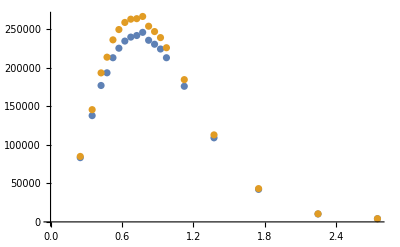

```mathematica
ListPlot[{Table[{murate2[[i,1]],murate2[[i,3]]/murate2[[i,2]]},{i,1,Length[murate2]}],Table[{murate3[[i,1]],murate3[[i,3]]/murate3[[i,2]]},{i,1,Length[murate3]}]}]
```

```mathematica
eapp=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-sig-ICARUS.dat","Data"];
```

```mathematica
eappc=Table[{eapp[[i,1]],(eapp[[i+1,2]]-eapp[[i,2]])},{i,1,Length[eapp],2}];
```

```mathematica
eappc
```

```mathematica
erate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-e.dat","Data"];
```

```mathematica
erate
```

{{0.275,0.15,355365,344766},{0.425,0.15,870575,844578},{0.575,0.15,1.40382×10^6,1.36185×10^6},{0.725,0.15,1.82503×10^6,1.77042×10^6},{0.875,0.15,2.01736×10^6,1.95697×10^6},{1.025,0.15,2.00177×10^6,1.94184×10^6},{1.2,0.2,2.36737×10^6,2.2965×10^6},{1.4,0.2,1.78968×10^6,1.73611×10^6},{1.625,0.25,1.3317×10^6,1.29187×10^6},{1.875,0.25,632283,613412},{2.5,1,613983,595750}}

```mathematica
Length[eappc]
```

11

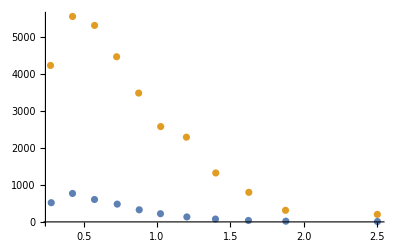

```mathematica
ListPlot[{eappc,Table[{erate[[i,1]],erate[[i,3]]},{i,1,Length[erate]}]},PlotRange->All]
```

```mathematica
Table[((eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[eappc]}]
```

{0.0184107,0.0207715,0.0171022,0.0161499,0.0140791,0.0128707,0.0117518,0.0116239,0.0120294,0.0153561,0.0476486}

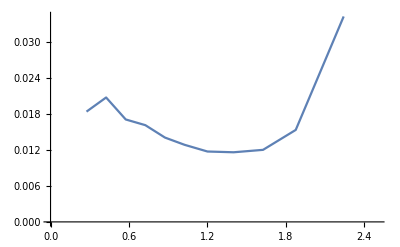

```mathematica
ListPlot[Table[{erate[[i,1]],(eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])},{i,1,Length[eappc]}],Joined->True]
```

```mathematica
ebg=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg-ICARUS.dat","Data"];
```

```mathematica
ebg
```

{{0.274866,423.077},{0.434581,826.923},{0.574332,1000},{0.734046,961.538},{0.878788,942.308},{1.02353,865.385},{1.19822,769.231},{1.40285,615.385},{1.62246,509.615},{1.87701,403.846},{2.50588,192.308}}

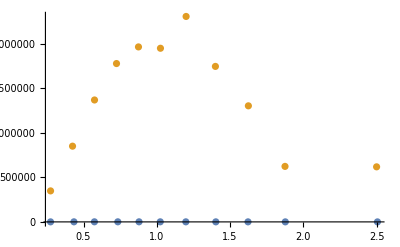

```mathematica
ListPlot[{ebg,Table[{erate[[i,1]],erate[[i,3]]},{i,1,Length[erate]}]},PlotRange->All]
```

```mathematica
Table[((ebg[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[ebg]}]
```

{0.0158104,0.0176645,0.0165265,0.0142228,0.0133468,0.0122348,0.0113838,0.00997164,0.00945462,0.00922419,0.00796246}

```mathematica
ebg2=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg2-ICARUS.dat","Data"];
ebg2c=Table[{ebg2[[i,1]],(ebg2[[i+1,2]]-ebg2[[i,2]])},{i,1,Length[ebg2],2}];
```

```mathematica
Length[ebg2c]
```

7

```mathematica
Table[((ebg2c[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[ebg2c]}]
```

{0.0000324693,0.0000115971,5.13708×10^-6,2.37088×10^-6,2.14484×10^-6,2.16155×10^-6,1.62465×10^-6}